# Helmholtz equation in spherical coordinates

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["spectral`","./spectral.m"];
Needs["sprouts`","./sprouts.m"];
```

```mathematica
ℒ={ϕ[0,0]''[r]+2/r ϕ[0,0]'[r]-(0(0+1))/r^2 ϕ[0,0][r]==-λ ϕ[0,0][r]};
ℬ={ϕ[0,0][1]==0};
𝒱={ϕ[0,0]};
```

```mathematica
A=SproutsFun[Join[ℒ,ℬ],𝒱,{r,0,1},40,eigenvalue->λ]
```

partition of the spatial domain :  {{0,1}}

regularity conditions will be enforced at r=0 based on indices of spherical harmonics

eigenvalue problem of type :   (A0+A1 λ)x==0

Size of output matrices :  20x20

{SparseArray[…],SparseArray[…]}

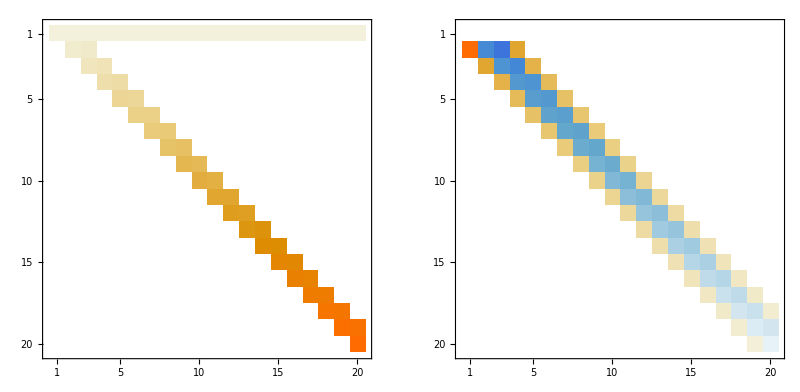

```mathematica
GraphicsRow[MatrixPlot/@A]
```

```mathematica
Sort@Eigenvalues[{A⟦1⟧,-A⟦2⟧}]//Sqrt
```

{3.14159,6.28319,9.42478,12.5664,15.708,18.8496,21.9911,25.1327,28.2743,31.4167,34.5536,37.8035,41.3975,46.7313,53.6365,65.9317,82.7851,123.663,201.053,∞}

```mathematica
(*analytical solutions *)
Table[BesselJZero[1/2,i],{i,1,20}]//N
```

{3.14159,6.28319,9.42478,12.5664,15.708,18.8496,21.9911,25.1327,28.2743,31.4159,34.5575,37.6991,40.8407,43.9823,47.1239,50.2655,53.4071,56.5487,59.6903,62.8319}